## Fixed M_Z'=10 TeV, Fixed Brane parameter = 0, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 ( (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime10=10;
MassNu=0.1;
CvL0=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.0)
```

-0.000128959

```mathematica
Zprime10decayfixedmass0[CvR_]:=MassZprime10/(12π)(1/4(CvL0+CvR)^2+1/4(CvL0-CvR)^2+2(MassNu/MassZprime10)^2(1/4(CvL0+CvR)^2-1/2(CvL0+CvR)^2))√(1-4(MassNu/MassZprime10)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime10decayfixedmass0Table=Table[{Q[i],Zprime10decayfixedmass0[Q[i]]},{i,0,Npt}]
```

{{0.,2.20501×10^-6},{0.1,1.3259},{0.2,5.30358},{0.3,11.933},{0.4,21.2143},{0.5,33.1473},{0.6,47.7322},{0.7,64.9688},{0.8,84.8572},{0.9,107.397},{1.,132.589}}

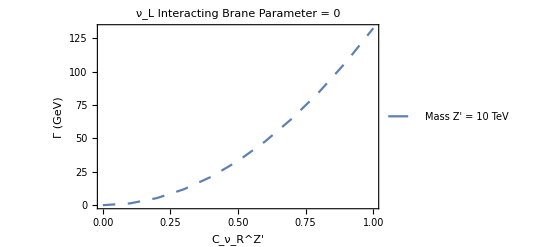

```mathematica
PlotZprimeDecayFixed100=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"Mass Z' = 10 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm["ν_L Interacting Brane Parameter = 0"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

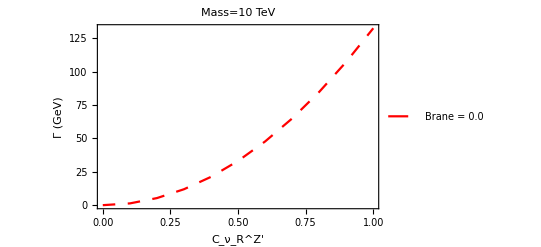

```mathematica
PlotZprimeDecayFixed100B=ListPlot[%%, Joined-> True,PlotStyle->{Red,Dashing[Medium]},PlotLegends->{"Brane = 0.0"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 10 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime10decayfixedmass0Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 2.20501×10^-6
0.1 | 1.3259
0.2 | 5.30358
0.3 | 11.933
0.4 | 21.2143
0.5 | 33.1473
0.6 | 47.7322
0.7 | 64.9688
0.8 | 84.8572
0.9 | 107.397
1. | 132.589

## Fixed M_Z'=8 TeV, Fixed Brane parameter = 0, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime8=8;
MassNu=0.1;
CvL0=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.0)
```

-0.000128959

```mathematica
Zprime8decayfixedmass0[CvR_]:=MassZprime8/(12π)(1/4(CvL0+CvR)^2+1/4(CvL0-CvR)^2+2(MassNu/MassZprime8)^2(1/4(CvL0+CvR)^2-1/2(CvL0+CvR)^2))√(1-4(MassNu/MassZprime8)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime8decayfixedmass0Table=Table[{Q[i],Zprime8decayfixedmass0[Q[i]]},{i,0,Npt}]
```

{{0.,1.76371×10^-6},{0.1,1.06054},{0.2,4.24214},{0.3,9.54482},{0.4,16.9686},{0.5,26.5134},{0.6,38.1793},{0.7,51.9662},{0.8,67.8743},{0.9,85.9034},{1.,106.054}}

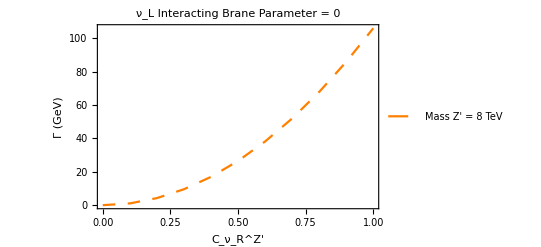

```mathematica
PlotZprimeDecayFixed80=ListPlot[%, Joined-> True,PlotStyle->{Orange, Dashing[Medium]},PlotLegends->{"Mass Z' = 8 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm["ν_L Interacting Brane Parameter = 0"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

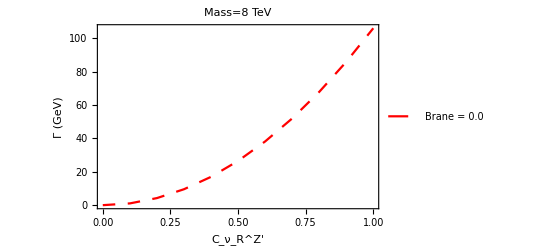

```mathematica
PlotZprimeDecayFixed80B=ListPlot[%%, Joined-> True,PlotStyle->{Red,Dashing[Medium]},PlotLegends->{"Brane = 0.0"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 8 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime8decayfixedmass0Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 1.76371×10^-6
0.1 | 1.06054
0.2 | 4.24214
0.3 | 9.54482
0.4 | 16.9686
0.5 | 26.5134
0.6 | 38.1793
0.7 | 51.9662
0.8 | 67.8743
0.9 | 85.9034
1. | 106.054

## Fixed M_Z'=5 TeV, Fixed Brane parameter = 0, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime5=5;
MassNu=0.1;
CvL0=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.0)
```

-0.000128959

```mathematica
Zprime5decayfixedmass0[CvR_]:=MassZprime5/(12π)(1/4(CvL0+CvR)^2+1/4(CvL0-CvR)^2+2(MassNu/MassZprime5)^2(1/4(CvL0+CvR)^2-1/2(CvL0+CvR)^2))√(1-4(MassNu/MassZprime5)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime5decayfixedmass0Table=Table[{Q[i],Zprime5decayfixedmass0[Q[i]]},{i,0,Npt}]
```

{{0.,1.10151×10^-6},{0.1,0.662352},{0.2,2.6494},{0.3,5.96115},{0.4,10.5976},{0.5,16.5588},{0.6,23.8446},{0.7,32.4551},{0.8,42.3904},{0.9,53.6503},{1.,66.235}}

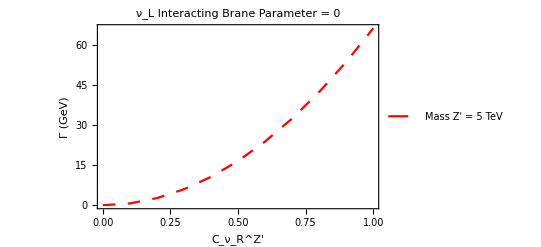

```mathematica
PlotZprimeDecayFixed50=ListPlot[%, Joined-> True,PlotStyle->{Red, Dashing[Medium]},PlotLegends->{"Mass Z' = 5 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm["ν_L Interacting Brane Parameter = 0"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

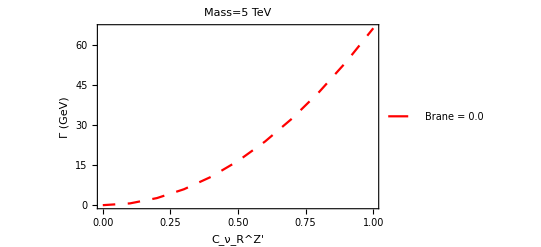

```mathematica
PlotZprimeDecayFixed50B=ListPlot[%%, Joined-> True,PlotStyle->{Red,Dashing[Medium]},PlotLegends->{"Brane = 0.0"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 5 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime5decayfixedmass0Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 1.10151×10^-6
0.1 | 0.662352
0.2 | 2.6494
0.3 | 5.96115
0.4 | 10.5976
0.5 | 16.5588
0.6 | 23.8446
0.7 | 32.4551
0.8 | 42.3904
0.9 | 53.6503
1. | 66.235

## OverLay

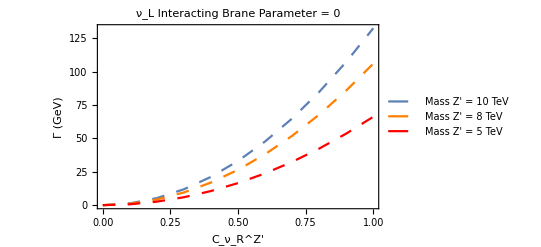

```mathematica
Show[PlotZprimeDecayFixed100,PlotZprimeDecayFixed80,PlotZprimeDecayFixed50]
```

## OverLay 2

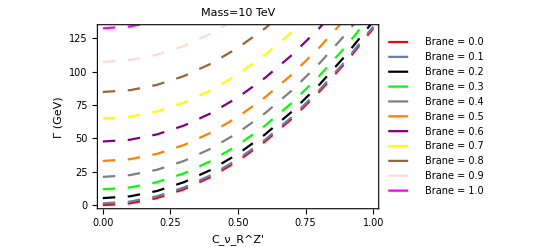

```mathematica
Show[PlotZprimeDecayFixed100B,PlotZprimeDecayFixed1001B,PlotZprimeDecayFixed1002B,PlotZprimeDecayFixed1003B,PlotZprimeDecayFixed1004B,PlotZprimeDecayFixed1005B,PlotZprimeDecayFixed1006B,PlotZprimeDecayFixed1007B,PlotZprimeDecayFixed1008B,PlotZprimeDecayFixed1009B,PlotZprimeDecayFixed101B]
```

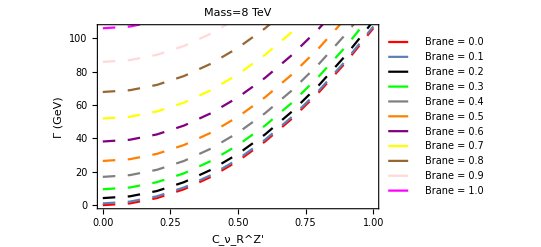

```mathematica
Show[PlotZprimeDecayFixed80B,PlotZprimeDecayFixed801B,PlotZprimeDecayFixed802B,PlotZprimeDecayFixed803B,PlotZprimeDecayFixed804B,PlotZprimeDecayFixed805B,PlotZprimeDecayFixed806B,PlotZprimeDecayFixed807B,PlotZprimeDecayFixed808B,PlotZprimeDecayFixed809B,PlotZprimeDecayFixed81B]
```

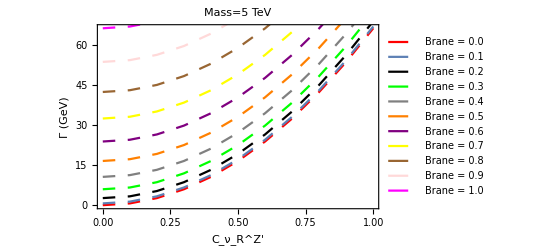

```mathematica
Show[PlotZprimeDecayFixed50B,PlotZprimeDecayFixed501B,PlotZprimeDecayFixed502B,PlotZprimeDecayFixed503B,PlotZprimeDecayFixed504B,PlotZprimeDecayFixed505B,PlotZprimeDecayFixed506B,PlotZprimeDecayFixed507B,PlotZprimeDecayFixed508B,PlotZprimeDecayFixed509B,PlotZprimeDecayFixed51B]
```